# Monte Carlo Integration

Created by Haroon Sakhi

## ✨ Introduction

Monte Carlo integration is a numerical technique that estimates the area under a curve using random sampling. It is part of the broader Monte Carlo methods, which rely on probability and large sample sizes to solve complex numerical problems.

## 🔢 Problem Setup

Suppose we have a function f(x) representing a curve, and we want to find the area under this curve

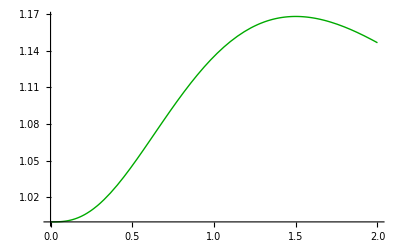

```mathematica
Plot[1+x^3Exp[-2 x],{x,0,2},PlotStyle->{Thick,Darker[Green]}]
```

In many cases, direct analytical integration is either impossible or impractical. For such situations, numerical approaches like Monte Carlo integration provide an alternative solution:

## 📍 Monte Carlo Integration

The method begins by enclosing the curve within a rectangular boundary. The choice of the rectangle’s dimensions is crucial, as it should be as tight as possible to ensure efficiency

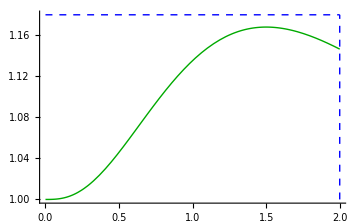

```mathematica
f[x_]:=1+x^3Exp[-2 x]

xMin=0;
xMax=2;
yMin=1;
yMax=1.18;

Show[Plot[f[x],{x,xMin,xMax},PlotStyle->{Thick,Darker[Green]}],
Graphics[{Dashed,Blue,Line[{{xMin,yMax},{xMax,yMax}}],(*Top horizontal line*)Line[{{xMax,yMin},{xMax,yMax}}]  (*Right vertical line*)}],
Axes->True,AxesOrigin->{0,0},PlotRange->{{xMin,xMax},{yMin,yMax}},ImageSize->Medium]
```

The ratio between the area of the rectangle  and the area under the curve  remains constant, if we do not change the domain of the curve and the rectangle’s dimensions :

Similarly, if we randomly generate  points within the rectangle, and  of those fall under the curve, then:

Equating these expressions, we derive:

Since the area of a rectangle is given by  , the formula simplifies to:

## 🛠️ Algorithm

To implement Monte Carlo integration, we follow these steps:

Define the function .

Determine the dimensions of the enclosing rectangle.

Generate  random points within the rectangle.

Count how many points  fall below .

Compute the area using  .

## 📌 Example Problem

### 🔷 Defining the Function .

Consider the function:

```mathematica
f[x_]:=Exp[-2 x]
```

#### 📊 Visualization

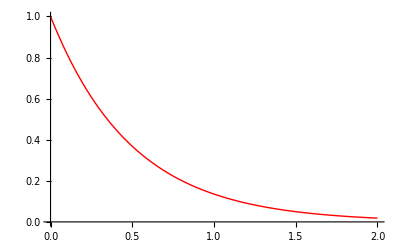

```mathematica
Plot[Exp[-2 x],{x,0,2},PlotStyle->{Thick,Red}]
```

### 🔷 Determining the rectangle dimensions

Let us find the area under this curve for domain  The maximum value of the curve in this domain is easy to figure out and is . Hence we will construct a rectangle of dimensions

```mathematica
length=2;
height=1;
totalPoints=100;
pointsUnderCurve=0;
```

#### 📊 Visualization

Which would look something like this,

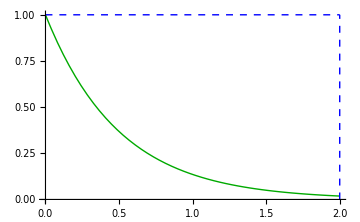

```mathematica
f[x_]:=Exp[-2 x]

xMin=0;
xMax=2;
yMin=0;
yMax=1;

Show[Plot[f[x],{x,xMin,xMax},PlotStyle->{Thick,Darker[Green]}],
Graphics[{Dashed,Blue,Line[{{xMin,yMax},{xMax,yMax}}],(*Top horizontal line*)Line[{{xMax,yMin},{xMax,yMax}}]  (*Right vertical line*)}],
Axes->True,AxesOrigin->{0,0},PlotRange->{{xMin,xMax},{yMin,yMax}},ImageSize->Medium]
```

### 🔷 Random Points

The area of the rectangle therefore would be 2. For simplicity let us generate a mere 100 points and see what ratio  do we get.

```mathematica
Do[x=RandomReal[{0,2}];
y=RandomReal[{0,1}];
If[y<f[x],pointsUnderCurve++],{totalPoints}];
```

### 📊 Results

After generation the answer we get for the area under the curve is,

```mathematica
area=length*height;
areaUnderCurve=area*(pointsUnderCurve/totalPoints);

Print["Estimated Area under the curve: ",areaUnderCurve];
```

Estimated Area under the curve: 23/50

## 🎯 Computational Efficiency in Mathematica

Mathematica provides several built-in features that optimize Monte Carlo simulations without the need for low-level programming, such as efficient random sampling, where its RandomReal[] function is optimized for high-performance random number generation—unlike Python, which struggles with large-scale Monte Carlo simulations due to its interpreted nature—while methods like BlockRandom ensure reproducibility in simulations.